# Hammersley Sofa

### Author

Eric W. Weisstein
February 27, 2025

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Laminae/HammersleySofa.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/HammersleySofa.html.

©2025 Wolfram Research, Inc. except for portions noted otherwise

## Optimal Hammersley sofa area

A086118

```mathematica
N[2/Pi+Pi/2,20]
```

2.2074160991624779623

## Figure

### Schematic

Click to copy:

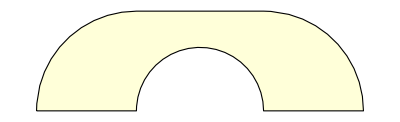

```mathematica
reg[0]:=Region@Disk[{0,0},1,{0,π}]
reg[0.]:=N[reg[0]]
reg[r_]:=RegionUnion[Disk[{-r,0},1,{Pi/2,π}],Disk[{r,0},1,{0,Pi/2}],RegionDifference[Rectangle[{-r,0},{r,1}],Disk[{0,0},r,{0,π}]]]
HammersleySofaRegion[r_]:=BoundaryDiscretizeRegion[reg[2/Pi],MeshCellStyle->{1->Black,2->LightYellow},MeshQualityGoal->"Maximal"]
HammersleySofaRegion[2/π]
```

```mathematica
HammersleySofaRegion[r_]:=Show[With[{sofa=DiscretizeRegion[reg[r],{PlotTheme->"SmoothShading",MeshCellStyle->LightYellow}]},
{sofa,DiscretizeRegion[RegionBoundary[sofa],MeshCellStyle->{1->Black,0->None}]}
]]
```

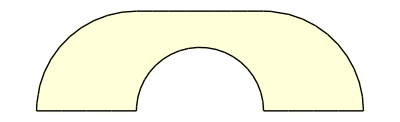

```mathematica
HammersleySofaRegion[2/π]
```

### Dimensioned

Click to copy:

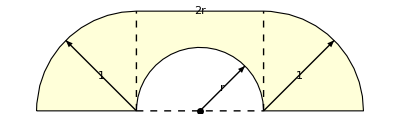

```mathematica
reg[0]:=Region@Disk[{0,0},1,{0,π}]
reg[0.]:=N[reg[0]]
reg[r_]:=RegionUnion[Disk[{-r,0},1,{Pi/2,π}],Disk[{r,0},1,{0,Pi/2}],RegionDifference[Rectangle[{-r,0},{r,1}],Disk[{0,0},r,{0,π}]]]
HammersleySofaRegion[r_]:=BoundaryDiscretizeRegion[reg[2/Pi],MeshCellStyle->{1->Black,2->LightYellow},MeshQualityGoal->"Maximal"]
With[{r=2/π},
Graphics[{HammersleySofaRegion[r],
{Dashed,Line[{{-r,0},{-r,1}}],Line[{{r,0},{r,1}}],Line[{{-r,0},{r,0}}]},
AbsolutePointSize[5],Point[{0,0}],
Arrowheads[.03],Arrow[{{0,0},r Through[{Cos,Sin}[45Degree]]}],Arrow[{{r,0},{r,0}+ Through[{Cos,Sin}[45Degree]]}],
Arrow[{{-r,0},{-r,0}+ Through[{Cos,Sin}[135Degree]]}],
Text[Row[{2,Style["r",Italic]}," "],{0,1},{0,-1.2}],Text[Row[{" ",Style["r",Italic]," "}],r/2 Through[{Cos,Sin}[45Degree]],Background->White],
Text[" 1 ",{r,0}+ Through[{Cos,Sin}[45Degree]]/2,Background->LightYellow],
Text[" 1 ",{-r,0}+ Through[{Cos,Sin}[135Degree]]/2,Background->LightYellow]
}]
]
```

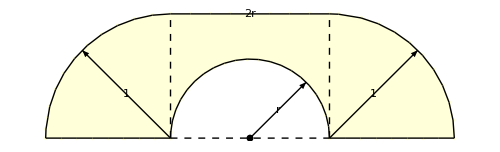

```mathematica
With[{r=2/π},
Graphics[{HammersleySofaRegion[r][[1]],
{Dashed,Line[{{-r,0},{-r,1}}],Line[{{r,0},{r,1}}],Line[{{-r,0},{r,0}}]},
AbsolutePointSize[5],Point[{0,0}],
Arrowheads[.03],Arrow[{{0,0},r Through[{Cos,Sin}[45Degree]]}],Arrow[{{r,0},{r,0}+ Through[{Cos,Sin}[45Degree]]}],
Arrow[{{-r,0},{-r,0}+ Through[{Cos,Sin}[135Degree]]}],
Text[Row[{2,Style["r",Italic]}," "],{0,1},{0,-1.2}],Text[Row[{" ",Style["r",Italic]," "}],r/2 Through[{Cos,Sin}[45Degree]],Background->White],
Text[" 1 ",{r,0}+ Through[{Cos,Sin}[45Degree]]/2,Background->LightYellow],
Text[" 1 ",{-r,0}+ Through[{Cos,Sin}[135Degree]]/2,Background->LightYellow]
},BaseStyle->Directive[FontFamily->"Times",14],ImageSize->500]
]
```

### Table as a function of r

Click to copy:

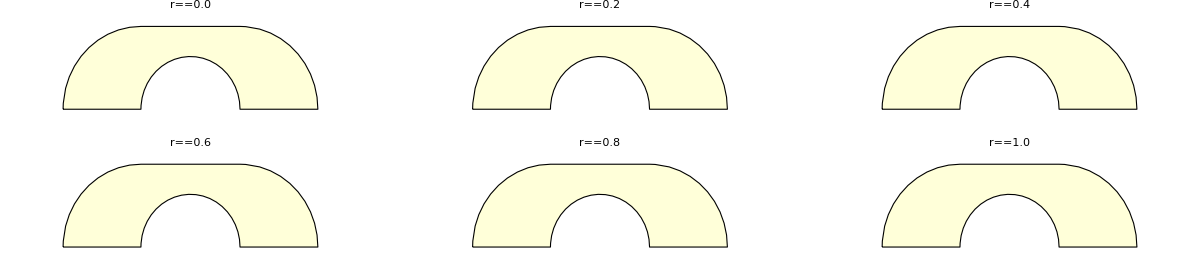

```mathematica
reg[0]:=Region@Disk[{0,0},1,{0,π}]
reg[0.]:=N[reg[0]]
reg[r_]:=RegionUnion[Disk[{-r,0},1,{Pi/2,π}],Disk[{r,0},1,{0,Pi/2}],RegionDifference[Rectangle[{-r,0},{r,1}],Disk[{0,0},r,{0,π}]]]
HammersleySofaRegion[r_]:=BoundaryDiscretizeRegion[reg[2/Pi],MeshCellStyle->{1->Black,2->LightYellow},MeshQualityGoal->"Maximal"]
GraphicsGrid[Partition[Table[Show[
HammersleySofaRegion[r],
PlotLabel->Row[{Style["r",Italic],"==",NumberForm[r,{2,1}]}," "],
PlotRange->{{-2,2},{-.1,1.1}}
],{r,0,1,.2}],3]]
```

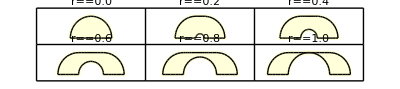

```mathematica
GraphicsGrid[Partition[Table[Show[
HammersleySofaRegion[r],
PlotLabel->Row[{Style["r",Italic],"==",NumberForm[r,{2,1}]}," "],
PlotRange->{{-2,2},{-.1,1.1}}
],{r,0,1,.2}],3],BaseStyle->InsetBoxOptions->{BaseStyle->Directive[Black,16,FontFamily->"Times"]},Dividers->All]
```

## Construction

### Romik (polygon approximation)

From Romik:

```mathematica
SofaDefaultNumSubdivisionPoints=50
```

50

```mathematica
HammersleyGeneralizedSofa[innerradius_]:={
  EdgeForm[{Black,AbsoluteThickness[1.5]}],
  SofaDefaultFillingColor,
  If[innerradius==0,SemicircleSofa,
    Polygon[
      Join[
        Table[{Cos[t],Sin[t]},{t,0,π/2,(π/2)/SofaDefaultNumSubdivisionPoints}],
        {{0,1},{-2innerradius,1}},
        Table[{-2innerradius+Cos[t],Sin[t]},{t,π/2,π,(π/2)/SofaDefaultNumSubdivisionPoints}],
        {{-2innerradius,0},{-2innerradius,0}},
        Table[{-innerradius+innerradius Cos[t],innerradius Sin[t]},
                   {t,π-π/Ceiling[innerradius SofaDefaultNumSubdivisionPoints],0,-π/Ceiling[innerradius SofaDefaultNumSubdivisionPoints]}]
      ]
    ]
  ]
}
```

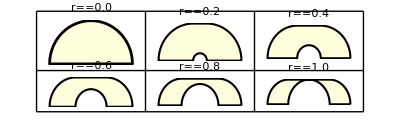

```mathematica
GraphicsGrid[Partition[Table[Graphics[
HammersleyGeneralizedSofa[r],
PlotLabel->Row[{Style["r",Italic],"==",NumberForm[r,{2,1}]}," "]
],{r,0,1,.2}],3],BaseStyle->InsetBoxOptions->{BaseStyle->Directive[Black,16,FontFamily->"Times"]},Dividers->All]
```

### FilledCurve

#### Built-in Circle

https://mail-archive.wolfram.com/archive/l-graphics/2024/Dec00/0027.html

```mathematica
HammersleySofaCurve[r_,a_]:=FilledCurve[{Circle[{-r,0},a,{Pi/2,Pi}],Line[{{-r-a,0},{-r,0}}],Circle[{0,0},r,{Pi,0}],Line[{{r,0},{r+a,0}}],Circle[{r,0},a,{0,Pi/2}]}]
```

```mathematica
HammersleySofaCurve[1,1]
```

FilledCurve[{Circle[{-1,0},1,{π/2,π}],Line[{{-2,0},{-1,0}}],Circle[{0,0},1,{π,0}],Line[{{1,0},{2,0}}],Circle[{1,0},1,{0,π/2}]}]

bug(455647): Support circular arcs in FilledCurve

```mathematica
Graphics[%]
```

-Graphics-

Need to convert Circle quadrants to Bezier/B-spline curves

#### ResourceFunction["SplineCircle"] using direct Circle replacement

Submitted a WFR comment 2024-12-17 direct circle replacement be made to work.  Requested it again in:

https://mail-archive.wolfram.com/archive/l-graphics/2024/Dec00/0031.html

```mathematica
HammersleySofaCurve1[r_,a_]:={Circle[{-r,0},a,{Pi/2,Pi}],Line[{{-r-a,0},{-r,0}}],Circle[{0,0},r,{Pi,0}],Line[{{r,0},{r+a,0}}],Circle[{r,0},a,{0,Pi/2}]}/.Circle->ResourceFunction["SplineCircle"]
```

```mathematica
Graphics[HammersleySofaCurve1[1,1]]
```

-Graphics-

```mathematica
Graphics[FilledCurve@HammersleySofaCurve1[1,1]]
```

-Graphics-

#### ResourceFunction["SplineCircle"] adding extra u argument

https://mail-archive.wolfram.com/archive/l-graphics/2024/Dec00/0028.html

```mathematica
HammersleySofaCurve2[r_,a_]:={Circle[{-r,0},a,{Pi/2,Pi}],Line[{{-r-a,0},{-r,0}}],Circle[{0,0},r,{Pi,0}],Line[{{r,0},{r+a,0}}],Circle[{r,0},a,{0,Pi/2}]}/.Circle[ctr_,rad_,q_]:>ResourceFunction["SplineCircle"][ctr,rad,{1,0},q]
```

```mathematica
Graphics[HammersleySofaCurve2[2/π,1]]
```

-Graphics-

```mathematica
Graphics[FilledCurve@HammersleySofaCurve2[2/π,1]]
```

-Graphics-

```mathematica
Graphics[{EdgeForm[Black],FaceForm[LightYellow],FilledCurve@HammersleySofaCurve2[2/π,1]}]
```

-Graphics-

Asked about in https://mail-archive.wolfram.com/archive/l-graphics/2024/Dec00/0031.html

Fixed in V2.0.1 of ResourceFunction["SplineCircle"]

#### ResourceFunction["SplineCircle"] adding extra u argument and top line segment

```mathematica
HammersleySofaCurve3[r_,a_]:={Circle[{-r,0},a,{Pi/2,Pi}],Line[{{-r-a,0},{-r,0}}],Circle[{0,0},r,{Pi,0}],Line[{{r,0},{r+a,0}}],Circle[{r,0},a,{0,Pi/2}],Line[{{r,a},{-r,a}}]}/.Circle[ctr_,rad_,q_]:>ResourceFunction["SplineCircle"][ctr,rad,{1,0},q]
```

```mathematica
Graphics[HammersleySofaCurve3[2/π,1]]
```

-Graphics-

```mathematica
Graphics[FilledCurve@HammersleySofaCurve2[2/π,1]]
```

-Graphics-

```mathematica
Graphics[{EdgeForm[Black],FaceForm[LightYellow],FilledCurve@HammersleySofaCurve3[2/π,1]}]
```

-Graphics-

Asked about in https://mail-archive.wolfram.com/archive/l-graphics/2024/Dec00/0031.html

Fixed in V2.0.1 of ResourceFunction["SplineCircle"]

#### BezierCircle from WA

From W|A CalculateUtilities`GraphicsUtilities`

```mathematica
bz[{x_,y_},r_,{a1_,a2_}]:=Module[{phi=a2-a1},AffineTransform[{{{Cos[a1],-Sin[a1]},{Sin[a1],Cos[a1]}},{x,y}}][r {{1,0},{1,4/3 Tan[phi/4]},{Cos[phi]+4/3 Tan[phi/4] Sin[phi],Sin[phi]-4/3 Tan[phi/4] Cos[phi]},{Cos[phi],Sin[phi]}}]]

BezierCircle[{x_,y_},r_,{a1_,a2_}]:=BezierCurve/@MapAt[Rest,bz[{x,y},r,#]&/@Partition[{a1,(3 a1+a2)/4,(a1+a2)/2,(a1+3 a2)/4,a2},2,1],{{2},{3},{4}}]

BezierCircle[{x_,y_},r_]:=BezierCircle[{x,y},r,{0,2Pi}]

If[!NameQ["System`DiskSegment"],DiskSegment[{x_,y_},r_,{a1_,a2_}]:=FilledCurve[BezierCircle[{x,y},r,{a1,a2}]]]

JoinSegments[first_,rest__]:=Join@Flatten[{first,DeleteFirstPoint/@{rest}}]

DeleteFirstPoint[{(h:BezierCurve|BSplineCurve|Line)[{_,b___}],r___}]:={h[{b}],r}
DeleteFirstPoint[(h:BezierCurve|BSplineCurve|Line)[{_,b___}]]:=h[{b}]
```

```mathematica
HammersleySofaCurve[r_,a_]:=JoinSegments@@({Circle[{-r,0},a,{Pi/2,Pi}],Line[{{-r-a,0},{-r,0}}],Circle[{0,0},r,{Pi,0}],Line[{{r,0},{r+a,0}}],Circle[{r,0},a,{0,Pi/2}]}/.Circle->BezierCircle)
```

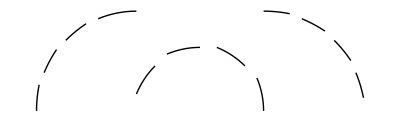

```mathematica
Graphics[{HammersleySofaCurve[2/π,1]}]
```

```mathematica
Graphics[{EdgeForm[Black],FaceForm[LightYellow],FilledCurve@HammersleySofaCurve[2/π,1]}]
```

-Graphics-

### RegionUnion

```mathematica
reg[0]:=Region@Disk[{0,0},1,{0,π}]
reg[0.]:=N[reg[0]]
reg[r_]:=RegionUnion[Disk[{-r,0},1,{Pi/2,π}],Disk[{r,0},1,{0,Pi/2}],
RegionDifference[Rectangle[{-r,0},{r,1}],Disk[{0,0},r,{0,π}]]]
```

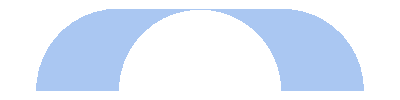

```mathematica
DiscretizeRegion[reg[1],PerformanceGoal->"Quality",MeshCellStyle->{1->None}]
```

```mathematica
DiscretizeRegion[reg[1],PerformanceGoal->"Quality",PlotTheme->"SmoothShading"]
```

-Graphics-

```mathematica
Manipulate[
Show[{
sofa=DiscretizeRegion[reg[r],{PlotTheme->"SmoothShading",MeshCellStyle->LightYellow}],
DiscretizeRegion[RegionBoundary[sofa],MeshCellStyle->{1->Black,0->None}]
},PlotRange->{{-2,2},{-.02,1.02}}],{r,0,1}]
```

```mathematica
HammersleySofaRegion[r_]:=Show[With[{sofa=DiscretizeRegion[reg[r],{PlotTheme->"SmoothShading",MeshCellStyle->LightYellow}]},
{sofa,DiscretizeRegion[RegionBoundary[sofa],MeshCellStyle->{1->Black,0->None}]}
]]
```

```mathematica
HammersleySofaRegion[2/Pi]
```

-Graphics-

### Inequalities

#### Assuming a==1

```mathematica
ineq[r_,{x_,y_}]:=Or[
(x+r)^2+y^2≤1&&x≤-r&&y≥0,
(x-r)^2+y^2<=1&&x≥r&&y≥0,
-r≤x≤r&&0<=y≤1&&x^2+y^2>r^2
]
```

```mathematica
ineq[r,{x,y}]//FullSimplify
```

(y≥0&&((x≥r&&(r-x)^2+y^2≤1)||(r+x≤0&&(r+x)^2+y^2≤1)))||(x^2+y^2>r^2&&0≤y≤1&&-r≤x≤r)

```mathematica
impl[r_,{x_,y_}]:=ImplicitRegion[ineq[r,{x,y}],{x,y}]
```

```mathematica
Manipulate[DiscretizeRegion[impl[r,{x,y}],PlotTheme->"SmoothShading"],{{r,2./Pi},0,1}]
```

-Graphics-

#### General

```mathematica
ineq[a_,r_,{x_,y_}]:=Or[
(x+r)^2+y^2≤a^2&&x≤-r&&y≥0,
(x-r)^2+y^2≤a^2&&x≥r&&y≥0,
-r≤x≤r&&0<=y≤a&&x^2+y^2>r^2
]
```

```mathematica
ineq[1,r,{x,y}]==ineq[r,{x,y}]
```

True

```mathematica
ineq[a,r,{x,y}]//FullSimplify
```

(y≥0&&((x≥r&&(r-x)^2+y^2≤a^2)||(r+x≤0&&(r+x)^2+y^2≤a^2)))||(x^2+y^2>r^2&&0≤y≤a&&-r≤x≤r)

## Animation

#### From movingsofas-v1 .3.nb

From Dan Romik's SofaVisualizationGeneralizedHammersleySofasInHallway routine in movingsofas-v1 .3.nb

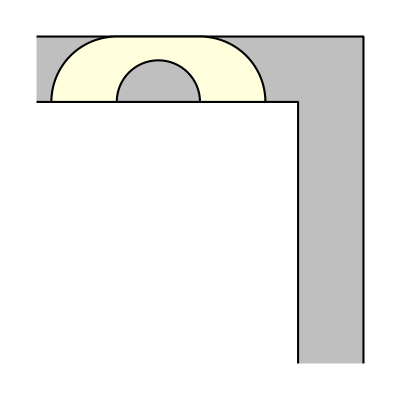
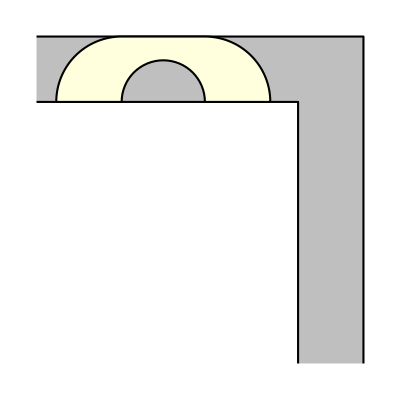
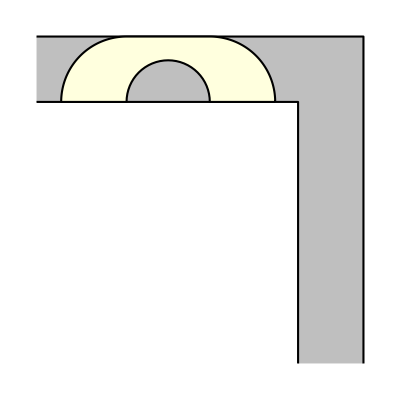
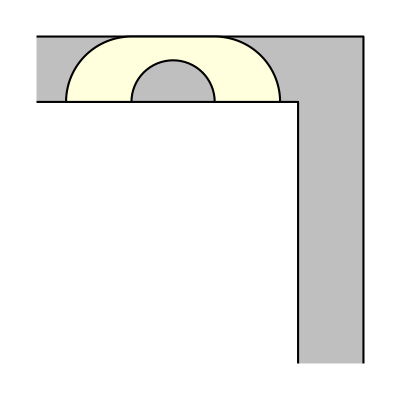
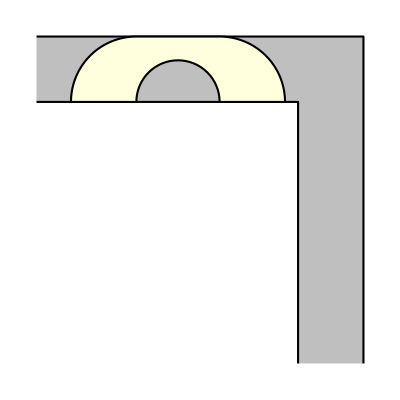
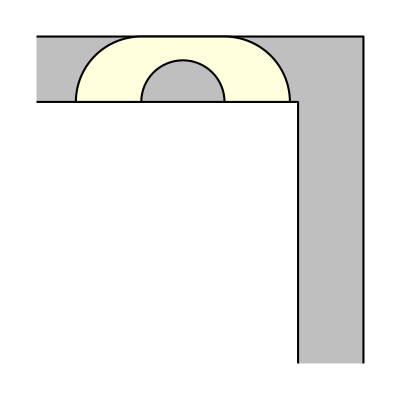
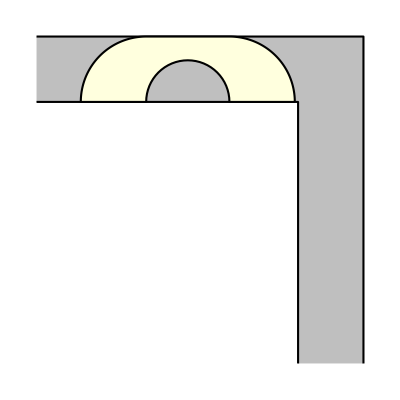
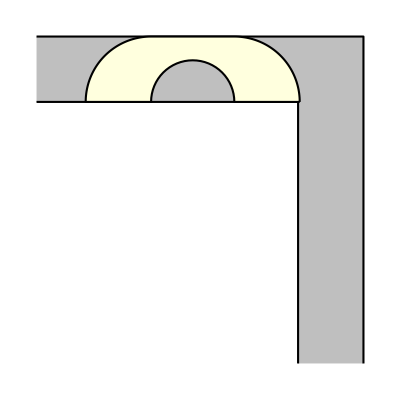

```mathematica
HammersleySofaAnimation=With[{r=2/π},Table[SofaMovieWithHallway[Max[4,2.5+2r],1.5,HammersleyGeneralizedSofa[r],HammersleyGeneralizedSofaRotationPath[r],t],{t,0,3,.05}]]
```

```mathematica
ListAnimate[HammersleySofaAnimation]
```

```mathematica
(gif=Export[FileNameJoin[{"/Users/eww/Sites/mathworld.wolfram.com/htdocs/images/gifs","MovingSofaHammersleyAnimation.gif"}],HammersleySofaAnimation,ImageSize->150])//AbsoluteTiming
```

{10.0116,/Users/eww/Sites/mathworld.wolfram.com/htdocs/images/gifs/MovingSofaHammersleyAnimation.gif}

```mathematica
Tally[ImageDimensions/@Import[gif]]
```

{{{150,150},61}}

#### Romik's website

https://www.math.ucdavis.edu/~romik/movingsofa/

```mathematica
ListAnimate[Import["https://www.math.ucdavis.edu/~romik/data/uploads/images/movingsofa/hammersley-movie.gif"]]
```

#### Wikipedia

https://commons.wikimedia.org/wiki/File:Hammersley_sofa_animated.gif

```mathematica
ListAnimate[Import["https://upload.wikimedia.org/wikipedia/commons/c/c1/Hammersley_sofa_animated.gif"]]
```

## Properties

### Area

#### r == 0 (semicircle)

```mathematica
Area[reg[0]]
```

π/2

#### r==r^*

```mathematica
Area[reg[2/π]]//Simplify//Timing
```

{5.26622,2/π+π/2}

#### r == 1 (connected at tip)

```mathematica
Area[reg[1]]//Timing
```

2

#### Symbolic r by hand

```mathematica
Collect[π/2+2r-(π r^2)/2,Pi]
```

2 r+π (1/2-r^2/2)

```mathematica
Limit[2 r+π (1/2-r^2/2),r->0]
```

π/2

```mathematica
2 r+π/2(1-r^2)
```

```mathematica
a^2(2 r/a+π/2(1-(r/a)^2))//Simplify
```

1/2 (a^2 π+4 a r-π r^2)

#### Symbolic r Boole Integrate with a == 1

```mathematica
Assuming[0<r<1,FullSimplify@Integrate[Boole[ineq[r,{x,y}]],{x,y}∈FullRegion[2]]]//Timing
```

{83.185,1/2 (π+4 r-π r^2)}

#### Symbolic r Boole Integrate with symbolic a

```mathematica
Assuming[0<r<a&&a>0,FullSimplify@Integrate[Boole[ineq[a,r,{x,y}]],{x,y}∈FullRegion[2]]]//Timing
```

{253.238,1/2 (a^2 π+4 a r-π r^2)}

#### Symbolic r Area

```mathematica
Subtract@@@Table[{Area[reg[r]],2 r+π (1/2-r^2/2)},{r,0,1,.1}]//Chop
```

{0,8.30319×10^-9,1.98881×10^-8,-1.85662×10^-9,7.23326×10^-10,-9.90168×10^-10,-7.34631×10^-10,0,-1.39319×10^-9,-1.01308×10^-9,-5.96534×10^-10}

```mathematica
TimeConstrained[Assuming[Area[reg[r]],0<r<1],10]//Timing
```

{8.39351,$Aborted}

#### Largest area

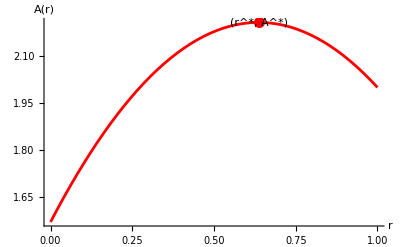

```mathematica
Plot[π/2+2r-(π r^2)/2,{r,0,1},PlotStyle->Red,BaseStyle->Directive[FontFamily->"Times",12,Black],AxesLabel->{r,A[r]},LabelStyle->Directive[Black,18],Epilog->{AbsolutePointSize[8],Style[Text[Row[{"(",SuperStar[r],", ",SuperStar[A],")"}],{2/π,2/π+π/2},{0,-2}],16],Red,Point[{2/π,2/π+π/2}]},PlotRangePadding->{Automatic,{Automatic,.1}}]
```

```mathematica
Maximize[π/2+2r-(π r^2)/2,r]
```

{2/π+π/2,{r→2/π}}

```mathematica
N[%,20]
```

{2.2074160991624779623,{r→0.63661977236758134308}}

```mathematica
HammersleySofaRegion[2/π]
```

-Graphics-

### AreaMomentOfInertia

```mathematica
<<MathWorld`Curves`
```

```mathematica
AreaInertiaMatrix[{x,y},"CoordinateSystem"->"Cartesian"]
```

{{y^2,-x y},{-x y,x^2}}

```mathematica
Assuming[0<r<1,FullSimplify[Integrate[{{y^2,-x y},{-x y,x^2}}Boole[ineq[r,{x,y}]],{x,y}∈FullRegion[2]]]]//Timing
```

{1300.85,{{(2 r)/3-1/8 π (-1+r^4),0},{0,2/3 r (2+r^2)-1/8 π (-1-4 r^2+r^4)}}}

```mathematica
FullSimplify[a^4{{(2 r)/3-1/8 π (-1+r^4),0},{0,2/3 r (2+r^2)-1/8 π (-1-4 r^2+r^4)}}/.r->r/a]
```

{{1/24 (3 a^4 π+16 a^3 r-3 π r^4),0},{0,1/24 (3 a^4 π+32 a^3 r+12 a^2 π r^2+16 a r^3-3 π r^4)}}

### Centroid

```mathematica
Assuming[0<r<1,FullSimplify[1/(1/2 (π+4 r-π r^2))Integrate[{x,y}Boole[ineq[r,{x,y}]],{x,y}∈FullRegion[2]]]]//Timing
```

{216.245,{0,(4+6 r-4 r^3)/(3 π+12 r-3 π r^2)}}

```mathematica
a((4+6 r-4 r^3)/(3 π+12 r-3 π r^2)/.r->r/a)//Factor
```

(2 (2 a^3+3 a^2 r-2 r^3))/(3 (a^2 π+4 a r-π r^2))

```mathematica
{0,(2 (2 (a^3-r^3)+3 a^2 r))/(3 (π(a^2-r^2)+4 a r))}
```

```mathematica
{0,(2 (2 (a^3-r^3)+3 a^2 r))/(3 (π(a^2-r^2)+4 a r))}/.r->0
```

{0,(4 a)/(3 π)}

### LineOfSymmetryCount

```mathematica
<<Symmetry`
```

```mathematica
SymmetryTransformation[DiscretizeRegion@reg[1/2]]
```

TransformationGroup[{}]

(wrong)

### Perimeter

```mathematica
Factor[π +2+2r+π r]
```

(2+π) (1+r)

```mathematica
Limit[(π+2)(r+1),r->0]
```

2+π